```mathematica
SetDirectory["/Users/dubard/Documents/Projects/FlexibleNetwork"]
```

/Users/dubard/Documents/Projects/FlexibleNetwork

```mathematica
trainErrorRate = Import["stats/learning_curve_train"];
```

Plot::argr: "Plot called with 1 argument; 2 arguments are expected. (*ButtonBox[

```mathematica
testErrorRate = Import["stats/learning_curve_test"];
```

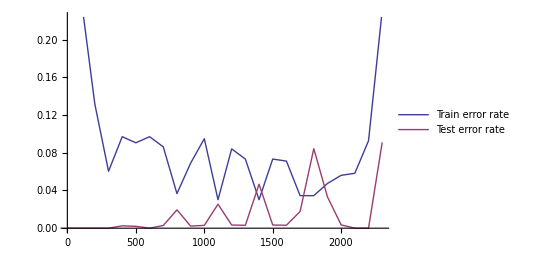

```mathematica
ListLinePlot[{trainErrorRate, testErrorRate}, PlotLegends->{"Train error rate", "Test error rate"}]
```

```mathematica
Export["figs/lc_error_rates.png", %56, ImageResolution->100]
```

figs/lc_error_rates.png

```mathematica
Import["figs/lc_error_rates.png"]
```

-Graphics-